```mathematica
Llist[g_,L_] := Table [ - g^2/(2) ,2 L] 
 Ldown[g_,L_] := DiagonalMatrix[Llist[g,L],1]
Lup[g_,L_] := DiagonalMatrix[Llist[g,L],-1]
LzLz[g_,L_] := DiagonalMatrix[Table[m^2 /(2g^2)+g^2,{m,-L, L }] ]
FluxPlaqOperator[g_,L_]  := LzLz[g,L]+  Ldown[g,L]+  Lup[g,L]
```

```mathematica
L=2;
U=DiagonalMatrix[Table [ 1,2L] ,1];
Udag=DiagonalMatrix[Table [ 1,2L] ,-1];
com=U.Udag-Udag.U;
comMat[g_]:=({evals, evecs}=Eigensystem[FluxPlaqOperator[g, L]];
evecs=(Normalize/@evecs[[Ordering[evals]]]);
Return[Table[evecs[[i]].com.evecs[[j]], {i, 1, 2L+1}, {j, 1, 2L+1}]];);
matlist=Table[comMat[g]//Abs, {g, 0.1, 5.0, 0.02}];
```

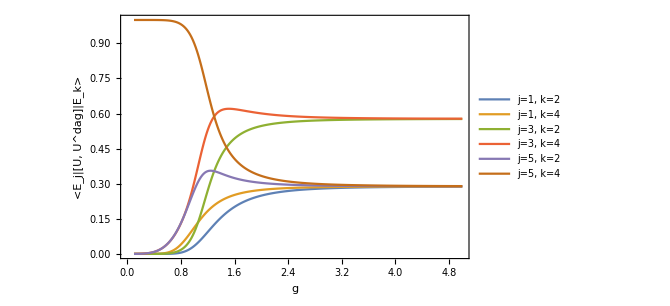

```mathematica
comElement[i_, j_]:=Transpose[{Table[g, {g, 0.1, 5.0, 0.02}], matlist[[All, i, j]]}]
ListPlot[{comElement[1, 2], comElement[1, 4], comElement[3, 2], comElement[3, 4], comElement[5, 2], comElement[5, 4]}, Joined->True, PlotLegends-> Placed[LineLegend[{"j=1, k=2", "j=1, k=4", "j=3, k=2", "j=3, k=4", "j=5, k=2", "j=5, k=4"}, LegendLayout->{"Row", 2}, LegendFunction->Framed], {0.7, 0.85}], FrameLabel->{"g", "<E_j|[U, U^dag]|E_k>"}, Frame->{{True, False}, {True, False}}]
```

```mathematica
comElement[1, 2]
```

Transpose::tperm: Permutation {1.17851×10^-13,1.05077×10^-12,6.68144×10^-12,3.31721×10^-11,1.36333×10^-10,«23»,1.51495×10^-9,4.3038×10^-9,1.12456×10^-8,2.73637×10^-8,«236»} is longer than the dimensions {246} of the expression.

```mathematica
Dimensions[matlist[[All, 1, 2]]]
```

{246}